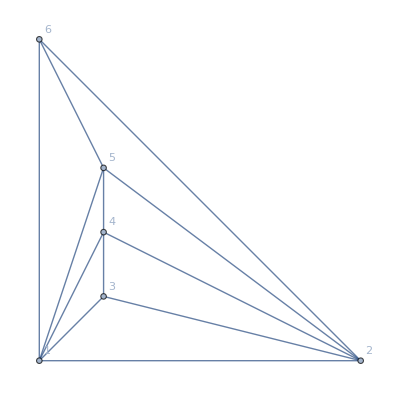

```mathematica
MinimalGraph[5]
```

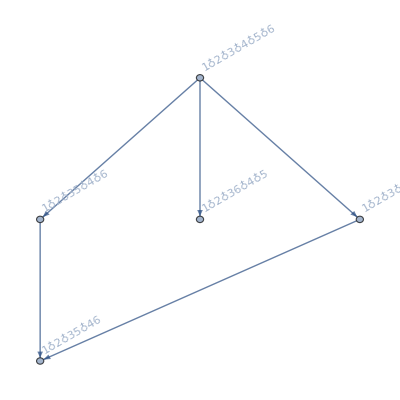

```mathematica
FormulaGraphReverse2[FindFullFormula[MinimalGraph[5]]]
```

```mathematica
nodes=With[{g=MinimalGraph[5]},
With [{full=FindFullFormula[g]},
Table[ImpliedNodes[Map[SymbolReplace[#,e]&,FindFullFormula[EdgeContract[g,e]]],full],{e,EdgeList[g]}]
]
]//Flatten//Tally
```

{{v1x2x3x4x5x6,12},{v1x2x3x46x5,6},{v1x2x36x4x5,8},{v1x2x35x4x6,6},{v1x2x35x46,1}}

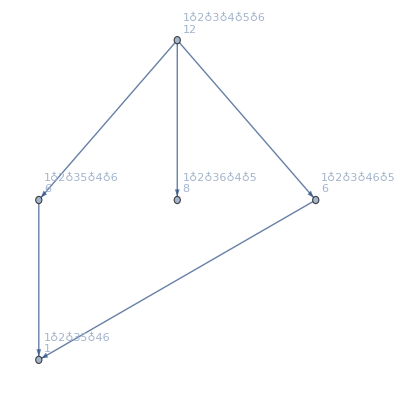

```mathematica
Block[{vert,graph},
vert=Map[First,nodes];
graph=Graph[FormulaGraphReverse2[vert],VertexLabels->Map[#[[1]]->Column[{SymbolToLabel[#[[1]]],Style[#[[2]],Red,Bold]},Center]&,nodes]];
graph
]
```

```mathematica
With[{g=MinimalGraph[5]},
With [{full=FindFullFormula[g]},
{FindFullFormula[EdgeContract[g,2<->3]],
full,
ImpliedNodes[FindFullFormula[EdgeContract[g,2<->3]],full]
}
]
]
```

{{v1x2x4x5x6,v1x2x46x5},{v1x2x3x4x5x6,v1x2x3x46x5,v1x2x36x4x5,v1x2x35x4x6,v1x2x35x46},{}}

```mathematica
DownSymbols[s_]:=Map[SetsToSymbol,FindCoarser[SymbolToSets[s]]];
```

```mathematica
DownSymbols[v1x2x3x4x5x6]
```

{v12x3x4x5x6,v13x2x4x5x6,v14x2x3x5x6,v15x2x3x4x6,v16x2x3x4x5,v1x23x4x5x6,v1x24x3x5x6,v1x25x3x4x6,v1x26x3x4x5,v1x2x34x5x6,v1x2x35x4x6,v1x2x36x4x5,v1x2x3x45x6,v1x2x3x46x5,v1x2x3x4x56}

```mathematica
UpSymbols[s_]:=Map[SetsToSymbol,FindFiner[SymbolToSets[s]]]
```

```mathematica
UpSymbols[v1x2x35x46]
```

{v1x2x3x46x5,v1x2x35x4x6}

```mathematica
CommonDownWards[symbols_]:=Block[{allDown={},result={}, up},
Table[
allDown=DeleteDuplicates[Join[allDown,DownSymbols[s]]],
{s,symbols}
];
allDown=DeleteDuplicates[allDown];
Table[
up=UpSymbols[down];
If[SubsetQ[symbols,up],AppendTo[result,down]]
,{down,allDown}
];
result
]
```

```mathematica
CommonDownWards[{v12x3x4x56x789,v1x2x34x56x789,v12x34x5x6x789}]
```

{}

```mathematica
CommonDownWards[{v1x2x3x46x5,v1x2x36x4x5,v1x2x35x4x6}]
```

{v1x2x35x46}

```mathematica
CountOfImplies [g_]:=Block[{nodes, full=FindFullFormula[g], vert,graph,rawNodes,byLevel,minLevel,minSymbols, vertexStyles={},addedSymbols={}, currentChallenge, currentLevel},
rawNodes=Flatten[Table[ImpliedNodes[Map[SymbolReplace[#,e]&,FindFullFormula[EdgeContract[g,e]]],full],{e,EdgeList[g]}]];
byLevel=Sort[Tally[Map[SymbolLevel,rawNodes]]];
nodes=Tally[rawNodes];
vert=Map[First,nodes];
minLevel=Min[Map[First,byLevel]];
currentLevel=VertexCount[g]-1;
minSymbols=Select[rawNodes,SymbolLevel[#]==currentLevel&];
currentChallenge=minSymbols;
While[currentChallenge≠{},
currentChallenge=CommonDownWards[currentChallenge];
currentLevel--;
currentChallenge=DeleteDuplicates[Join[currentChallenge,Select[rawNodes,SymbolLevel[#]==2&]]];
addedSymbols=Join[addedSymbols,currentChallenge]
];
vertexStyles=Join[Map[#->Red&,addedSymbols],Map[#->Green&,DeleteDuplicates[rawNodes]]];
graph=Graph[
FormulaGraphReverse2[full],
VertexLabels->Map[#[[1]]->Rotate[Column[{SymbolToLabel[#[[1]]],Style[#[[2]],Red,Bold]},Center],Pi/5]&,nodes],
VertexStyle->vertexStyles
];
Labeled[graph,byLevel]
]
```

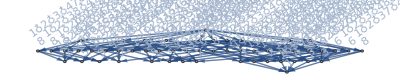
-Graphics-{{4,1},{5,51},{6,201},{7,132},{8,18}}

```mathematica
CountOfImplies[MinimalGraph[7]]
```

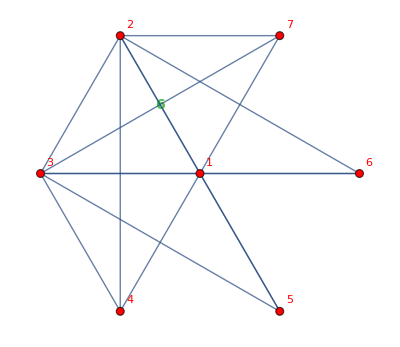
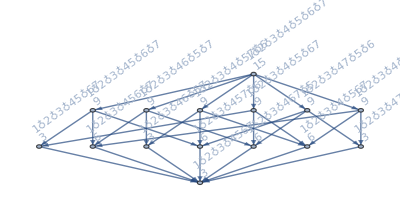
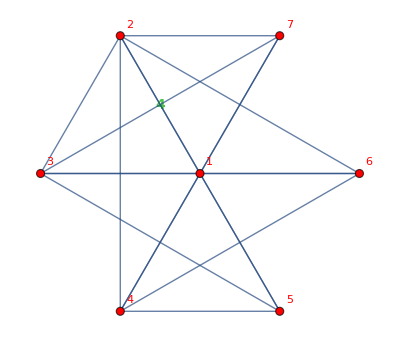
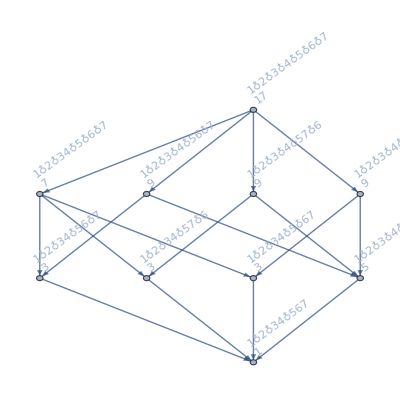
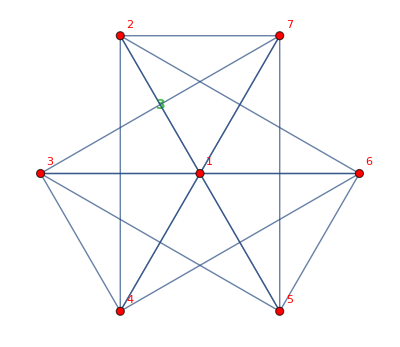
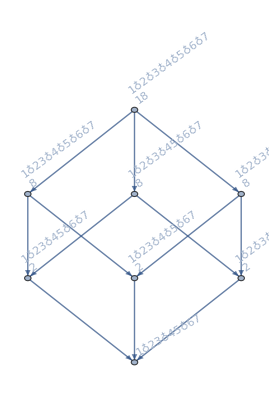
{-Graphics-→-Graphics-{{4,3},{5,33},{6,54},{7,15}},-Graphics-→-Graphics-{{4,1},{5,14},{6,34},{7,17}},-Graphics-→-Graphics-{{5,6},{6,24},{7,18}}}

```mathematica
Map[#->CountOfImplies[#]&,BarelyFourColorableGraphsOfCount[7]]
```

```mathematica
CountOfImplies[-Graphics-]
```

-Graphics-

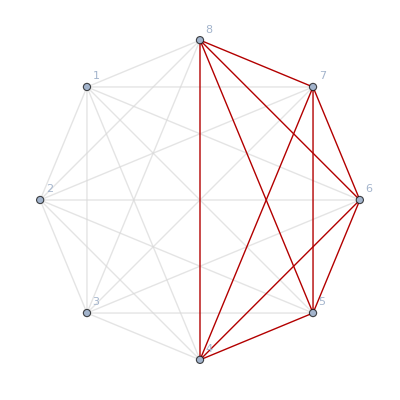
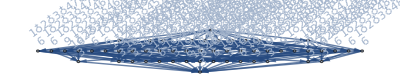
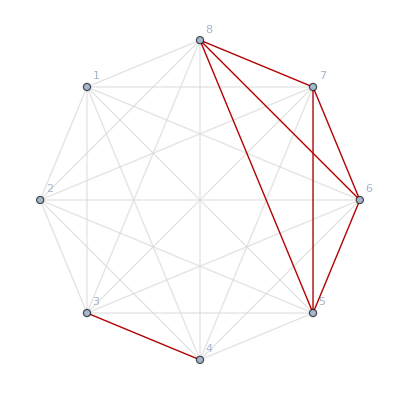
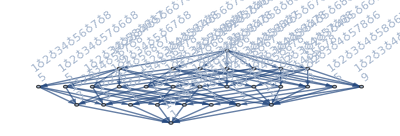
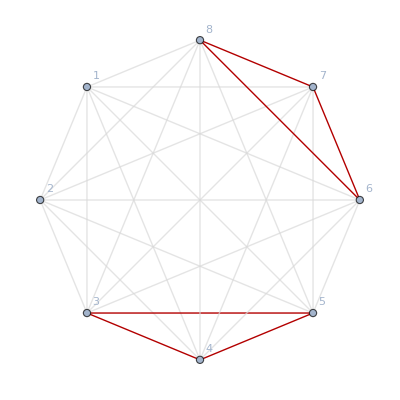
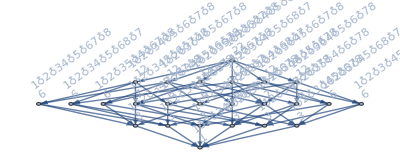
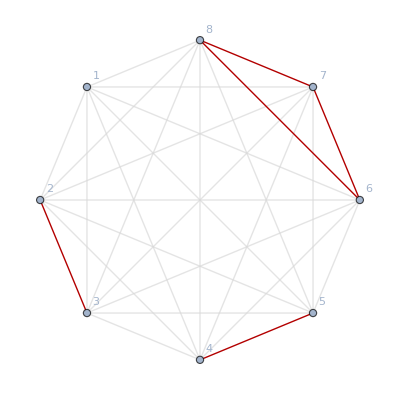
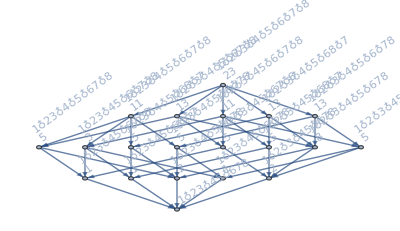
{-Graphics-→-Graphics-{{4,3},{5,60},{6,180},{7,120},{8,18}},-Graphics-→-Graphics-{{4,1},{5,20},{6,81},{7,87},{8,21}},-Graphics-→-Graphics-{{4,1},{5,18},{6,68},{7,72},{8,22}},-Graphics-→-Graphics-{{5,7},{6,41},{7,61},{8,23}},-Graphics-→-Graphics-{{6,24},{7,48},{8,24}}}

```mathematica
Map[BeautiGraph[#]->CountOfImplies[#]&,BarelyFourColorableGraphsOfCount[8]]
```

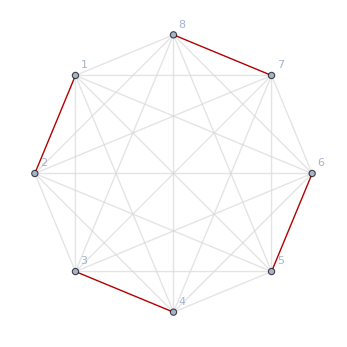
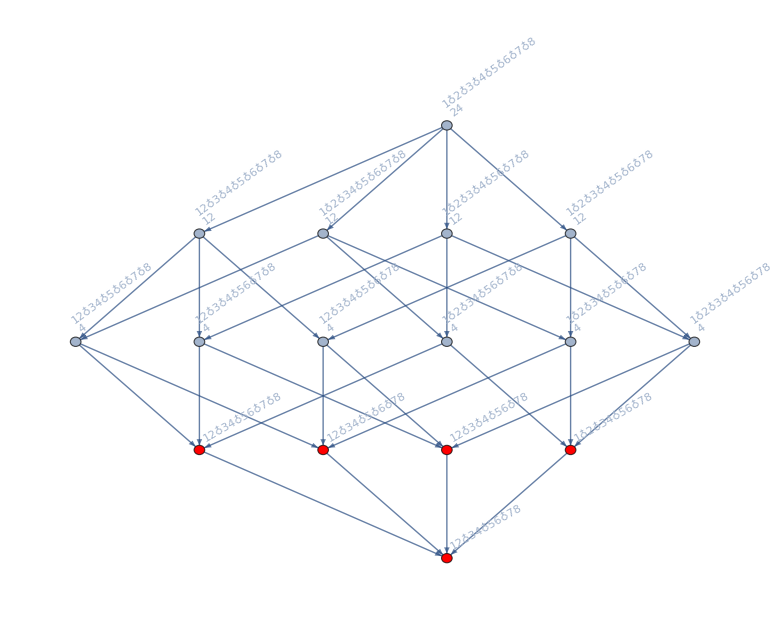
```mathematica
{-Graphics-->-Graphics-{{4,3},{5,60},{6,180},{7,120},{8,18}},-Graphics-->-Graphics-{{4,1},{5,20},{6,81},{7,87},{8,21}},-Graphics-->-Graphics-{{4,1},{5,18},{6,68},{7,72},{8,22}},-Graphics-->-Graphics-{{5,7},{6,41},{7,61},{8,23}},-Graphics-->-Graphics-{{6,24},{7,48},{8,24}}}
```

```mathematica
Map[Last,{{4,3},{5,33},{6,54},{7,15}}]
```

{3,33,54,15}

```mathematica
Map[FactorInteger,%]
```

{{{3,1}},{{3,1},{11,1}},{{2,1},{3,3}},{{3,1},{5,1}}}

```mathematica
PrimeQ[87]
```

False

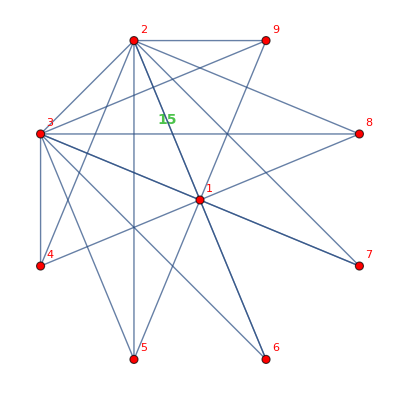
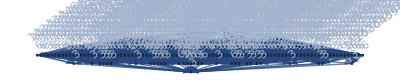
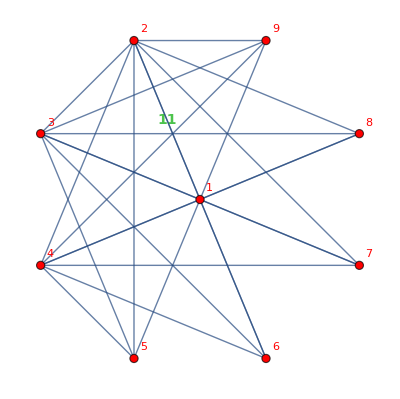
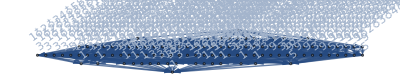
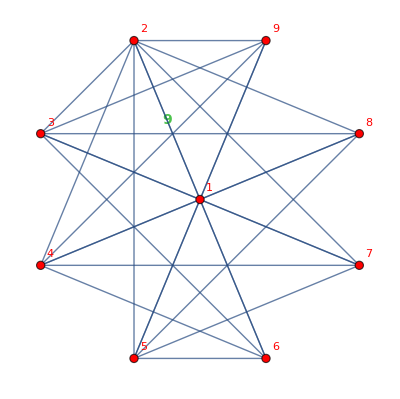
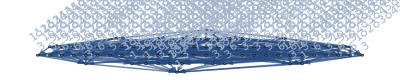
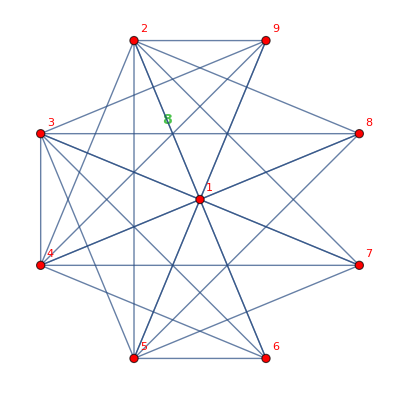
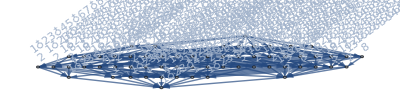
{-Graphics-→-Graphics-{{4,3},{5,111},{6,540},{7,645},{8,225},{9,21}},-Graphics-→-Graphics-{{4,1},{5,30},{6,190},{7,335},{8,181},{9,25}},-Graphics-→-Graphics-{{4,1},{5,24},{6,136},{7,240},{8,147},{9,27}},-Graphics-→-Graphics-{{5,8},{6,72},{7,176},{8,136},{9,28}},-Graphics-→-Graphics-{{5,8},{6,63},{7,145},{8,117},{9,29}},-Graphics-→-Graphics-{{6,30},{7,102},{8,102},{9,30}}}

```mathematica
Map[#->CountOfImplies[#]&,BarelyFourColorableGraphsOfCount[9]]
```

```mathematica
BeautiGraph[g_]:=CompleteGraph[VertexCount[g],GraphHighlight->EdgeList[GraphComplement[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name", EdgeStyle->LightGray]
```

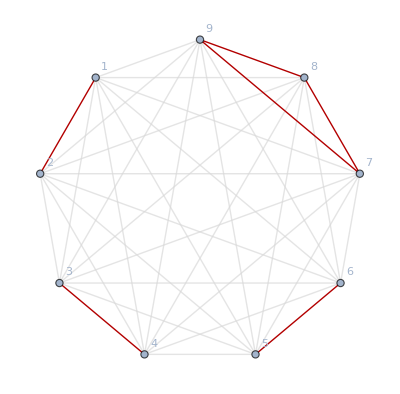

```mathematica
BeautiGraph[-Graphics-]
```

```mathematica
CountOfImplies[-Graphics-]
```

-Graphics-{{6,30},{7,102},{8,102},{9,30}}

```mathematica
CommonDownWards[{v12x3x4x56x789,v1x2x34x56x789,v12x34x5x6x789}]
```

{}

```mathematica
FindFullFormula[-Graphics-]
```

{v1x2x3x4x5x6x7x8x9,v1x2x3x4x5x6x7x89,v1x2x3x4x5x6x79x8,v1x2x3x4x5x6x78x9,v1x2x3x4x5x6x789,v1x2x3x4x56x7x8x9,v1x2x3x4x56x7x89,v1x2x3x4x56x79x8,v1x2x3x4x56x78x9,v1x2x3x4x56x789,v1x2x34x5x6x7x8x9,v1x2x34x5x6x7x89,v1x2x34x5x6x79x8,v1x2x34x5x6x78x9,v1x2x34x5x6x789,v1x2x34x56x7x8x9,v1x2x34x56x7x89,v1x2x34x56x79x8,v1x2x34x56x78x9,v1x2x34x56x789,v12x3x4x5x6x7x8x9,v12x3x4x5x6x7x89,v12x3x4x5x6x79x8,v12x3x4x5x6x78x9,v12x3x4x5x6x789,v12x3x4x56x7x8x9,v12x3x4x56x7x89,v12x3x4x56x79x8,v12x3x4x56x78x9,v12x3x4x56x789,v12x34x5x6x7x8x9,v12x34x5x6x7x89,v12x34x5x6x79x8,v12x34x5x6x78x9,v12x34x5x6x789,v12x34x56x7x8x9,v12x34x56x7x89,v12x34x56x79x8,v12x34x56x78x9,v12x34x56x789}

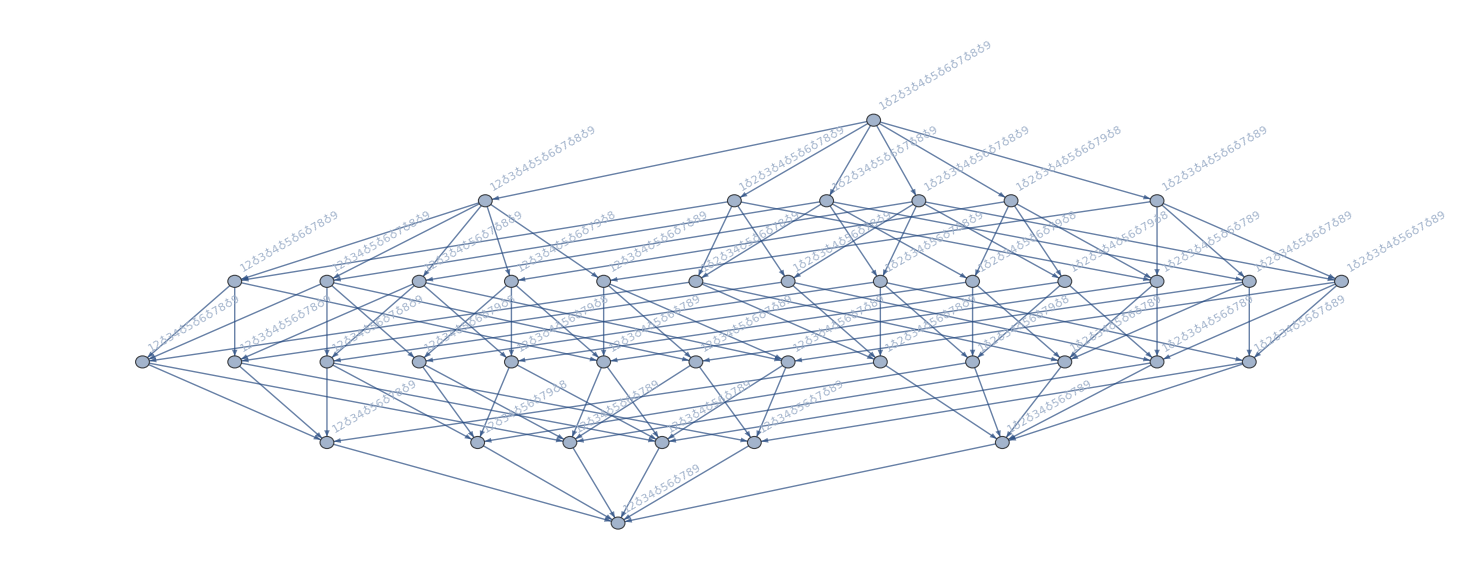

```mathematica
FormulaGraphReverse2[{v1x2x3x4x5x6x7x8x9,v1x2x3x4x5x6x7x89,v1x2x3x4x5x6x79x8,v1x2x3x4x5x6x78x9,v1x2x3x4x5x6x789,v1x2x3x4x56x7x8x9,v1x2x3x4x56x7x89,v1x2x3x4x56x79x8,v1x2x3x4x56x78x9,v1x2x3x4x56x789,v1x2x34x5x6x7x8x9,v1x2x34x5x6x7x89,v1x2x34x5x6x79x8,v1x2x34x5x6x78x9,v1x2x34x5x6x789,v1x2x34x56x7x8x9,v1x2x34x56x7x89,v1x2x34x56x79x8,v1x2x34x56x78x9,v1x2x34x56x789,v12x3x4x5x6x7x8x9,v12x3x4x5x6x7x89,v12x3x4x5x6x79x8,v12x3x4x5x6x78x9,v12x3x4x5x6x789,v12x3x4x56x7x8x9,v12x3x4x56x7x89,v12x3x4x56x79x8,v12x3x4x56x78x9,v12x3x4x56x789,v12x34x5x6x7x8x9,v12x34x5x6x7x89,v12x34x5x6x79x8,v12x34x5x6x78x9,v12x34x5x6x789,v12x34x56x7x8x9,v12x34x56x7x89,v12x34x56x79x8,v12x34x56x78x9,v12x34x56x789}]
```